# Initialization

```mathematica
HaToeV=27.21138602;
```

```mathematica
SetDirectory["~/Dropbox/Manuscripts/Tmatrix/Data"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}"}];
```

# Helium-like ions

#### H^-/aug-cc-pVQZ

```mathematica
H$AVQZ$BSEGW$1={3.544803,6.664916};
H$AVQZ$dBSEGW$1={3.477673,6.417843};
H$AVQZ$BSEGW$3={1.924462,5.015223};
H$AVQZ$dBSEGW$3={1.645051,4.641375};
```

```mathematica
H$AVQZ$BSEGT$1={3.076687,6.195034};
H$AVQZ$dBSEGT$1={3.238214,6.211650};
H$AVQZ$BSEGT$3={2.042753,4.455234};
H$AVQZ$dBSEGT$3={1.749067,4.467813};
```

```mathematica
H$AVQZ$FCI$1={2.92693343,5.91171092};
H$AVQZ$FCI$3={1.95653920,5.02369423};
```

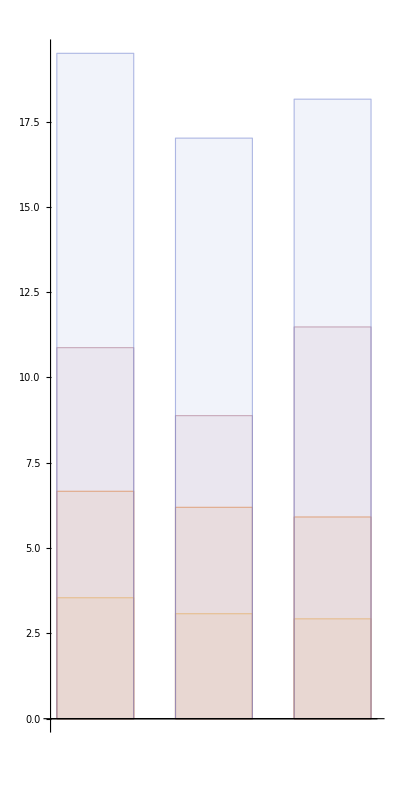

```mathematica
BarChart[{H$AVQZ$BSEGW$1,H$AVQZ$BSEGT$1,H$AVQZ$FCI$1},ChartLayout->"Overlapped",ChartStyle->Opacity[0.1],AspectRatio->2]
```

#### He/aug-cc-pVQZ

```mathematica
He$AVQZ$BSEGW$1={21.135455,24.260667};
He$AVQZ$dBSEGW$1={21.121553,24.217977};
He$AVQZ$BSEGW$3={19.829721,22.853260};
He$AVQZ$dBSEGW$3={19.747778,22.769397};
```

```mathematica
He$AVQZ$BSEGT$1={21.047638,24.358335};
He$AVQZ$dBSEGT$1={21.036042,24.307115};
He$AVQZ$BSEGT$3={20.000952,22.897296};
He$AVQZ$dBSEGT$3={19.958898,22.846260};
```

```mathematica
He$AVQZ$FCI$1={20.82451590,23.90793935};
He$AVQZ$FCI$3={19.87191393,23.00154067};
```

#### Li^+/aug-cc-pVQZ

```mathematica
Li$AVQZ$BSEGW$1={,,,};
Li$AVQZ$dBSEGW$1={,,,};
Li$AVQZ$BSEGW$3={,,,};
Li$AVQZ$dBSEGW$3={,,,};
```

```mathematica
Li$AVQZ$BSEGT$1={,,,};
Li$AVQZ$dBSEGT$1={,,,};
Li$AVQZ$BSEGT$3={,,,};
Li$AVQZ$dBSEGT$3={,,,};
```

```mathematica
Li$AVQZ$FCI$1={,,,};
Li$AVQZ$FCI$3={,,,};
```

# H_2/cc-pVDZ

## Singlets & Triplets

### Loading data

```mathematica
FCI1=Import["h2_cc-pvtz_fci_singlets.dat"];
BSE$GT1=Import["h2_cc-pvtz_bse@gt_singlets.dat"];
BSE$GW1=Import["h2_cc-pvtz_bse@gw_singlets.dat"];
dBSE$GT1=Import["h2_cc-pvtz_dbse@gt_singlets.dat"];
dBSE$GW1=Import["h2_cc-pvtz_dbse@gw_singlets.dat"];
```

```mathematica
FCI3=Import["h2_cc-pvtz_fci_triplets.dat"];
BSE$GT3=Import["h2_cc-pvtz_bse@gt_triplets.dat"];
BSE$GW3=Import["h2_cc-pvtz_bse@gw_triplets.dat"];
dBSE$GT3=Import["h2_cc-pvtz_dbse@gt_triplets.dat"];
dBSE$GW3=Import["h2_cc-pvtz_dbse@gw_triplets.dat"];
```

### Plotting stuff

```mathematica
singlets=Show[{
ListPlot[
{Callout[FCI1⟦;;,{1,2}⟧,"B ^1Σ_u^+"],Callout[FCI1⟦;;,{1,3}⟧,"F ^1Σ_g^+"],Callout[FCI1⟦;;,{1,4}⟧,"B' ^1Σ_u^+"],Callout[FCI1⟦;;,{1,5}⟧,"E ^1Σ_g^+"],Callout[FCI1⟦;;,{1,6}⟧,"C ^1Π_u"]}
,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},AspectRatio->1.5,PlotRange->{All,{5,30}},
FrameLabel->{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],MaTeX["\\text{Singlet excitation energy (eV)}",FontSize->20]},
ImageSize->400,PlotStyle->Directive[{Black,Opacity[0.7],Thickness[0.01]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{FCI}",FontSize->20]},GridLines->Automatic]
,
ListPlot[
{BSE$GW1⟦;;,{1,2}⟧,BSE$GW1⟦;;,{1,3}⟧,BSE$GW1⟦;;,{1,4}⟧,BSE$GW1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0W_0$}",FontSize->20]}]
,
ListPlot[
{BSE$GT1⟦;;,{1,2}⟧,BSE$GT1⟦;;,{1,3}⟧,BSE$GT1⟦;;,{1,4}⟧,BSE$GT1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20]}]
}]
```

-Graphics-

```mathematica
triplets=Show[{
ListPlot[
{Callout[FCI3⟦;;,{1,2}⟧,"b ^3Σ_u^+"],Callout[FCI3⟦;;,{1,3}⟧,"a ^3Σ_g^+"],Callout[FCI3⟦;;,{1,4}⟧,"e ^3Σ_u^+"],Callout[FCI3⟦;;,{1,5}⟧,"c ^3Π_u"]}
,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},AspectRatio->1.5,PlotRange->{All,{0,25}},
FrameLabel->{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],MaTeX["\\text{Triplet excitation energy (eV)}",FontSize->20]},
ImageSize->400,PlotStyle->Directive[{Black,Opacity[0.7],Thickness[0.01]}],PlotMarkers->"OpenMarkers",Joined->True,GridLines->Automatic]
,
ListPlot[
{BSE$GW3⟦;;,{1,2}⟧,BSE$GW3⟦;;,{1,3}⟧,BSE$GW3⟦;;,{1,4}⟧,BSE$GW3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True]
,
ListPlot[
{BSE$GT3⟦;;,{1,2}⟧,BSE$GT3⟦;;,{1,3}⟧,BSE$GT3⟦;;,{1,4}⟧,BSE$GT3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True]
}]
```

-Graphics-

```mathematica
Grid[{{singlets,triplets}}]
Export["H2.pdf",%];
```

-Graphics- | -Graphics-

### Gap

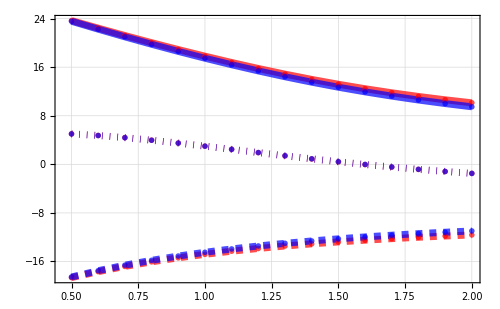

```mathematica
Gap=Import["h2_cc-pvtz_gap.dat"];ListPlot[{Gap⟦;;,{1,2}⟧,Gap⟦;;,{1,5}⟧,Gap⟦;;,{1,3}⟧,Gap⟦;;,{1,6}⟧,Gap⟦;;,{1,4}⟧,Gap⟦;;,{1,7}⟧},Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},PlotRange->{All,All},
FrameLabel->{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],MaTeX["\\text{One-electron energy (eV)}",FontSize->20]},
ImageSize->500,
PlotStyle->{{Red,Dashed,Opacity[0.7],Thickness[0.01]},{Blue,Dashed,Opacity[0.7],Thickness[0.01]},
{Red,Dotted,Opacity[0.7],Thickness[0.01]},{Blue,Dotted,Opacity[0.7],Thickness[0.01]},
{Red,Opacity[0.7],Thickness[0.01]},{Blue,Opacity[0.7],Thickness[0.01]}},
PlotMarkers->"OpenMarkers",Joined->True,
PlotLegends->{MaTeX["\\text{HOMO@$G_0W_0$}",FontSize->20],MaTeX["\\text{HOMO@$G_0T_0$}",FontSize->20],
MaTeX["\\text{LUMO@$G_0W_0$}",FontSize->20],MaTeX["\\text{LUMO@$G_0T_0$}",FontSize->20],
MaTeX["\\text{Gap@$G_0W_0$}",FontSize->20],MaTeX["\\text{Gap@$G_0T_0$}",FontSize->20]},
GridLines->Automatic]
Export["H2_gap.pdf",%];
```

### Dynamical correction

```mathematica
ΔBSE$GW1=Table[{FCI1⟦k,1⟧,FCI1⟦k,2⟧-BSE$GW1⟦k,2⟧},{k,Length[FCI1]}];
ΔdBSE$GW1=Table[{FCI1⟦k,1⟧,FCI1⟦k,2⟧-dBSE$GW1⟦k,2⟧},{k,Length[FCI1]}];
ΔBSE$GT1=Table[{FCI1⟦k,1⟧,FCI1⟦k,2⟧-BSE$GT1⟦k,2⟧},{k,Length[FCI1]}];
ΔdBSE$GT1=Table[{FCI1⟦k,1⟧,FCI1⟦k,2⟧-dBSE$GT1⟦k,2⟧},{k,Length[FCI1]}];
```

```mathematica
ΔBSE$GW3=Table[{FCI3⟦k,1⟧,FCI3⟦k,2⟧-BSE$GW3⟦k,2⟧},{k,Length[FCI3]}];
ΔdBSE$GW3=Table[{FCI3⟦k,1⟧,FCI3⟦k,2⟧-dBSE$GW3⟦k,2⟧},{k,Length[FCI3]}];
ΔBSE$GT3=Table[{FCI3⟦k,1⟧,FCI3⟦k,2⟧-BSE$GT3⟦k,2⟧},{k,Length[FCI3]}];
ΔdBSE$GT3=Table[{FCI3⟦k,1⟧,FCI3⟦k,2⟧-dBSE$GT3⟦k,2⟧},{k,Length[FCI3]}];
```

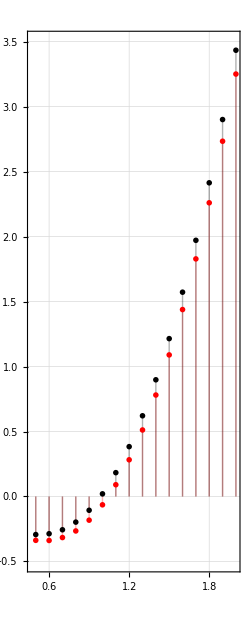
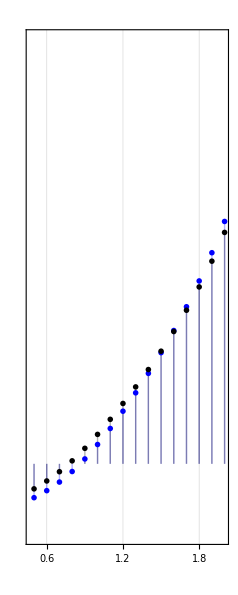

```mathematica
Row[{
ListPlot[{ΔBSE$GW1,ΔdBSE$GW1},Filling->Axis,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,12},PlotRange->{All,{-0.5,3.5}},AspectRatio->2.5,FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{MaTeX["\\text{Error wrt FCI for B $^1\\Sigma_u^+$ (eV)}",FontSize->20],None},{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],None}},
ImageSize->250,
PlotStyle->{Red,Black},
PlotMarkers->"OpenMarkers",
PlotLegends->Placed[{MaTeX["\\text{BSE@$G_0W_0$}",FontSize->20],MaTeX["\\text{dBSE@$G_0W_0$}",FontSize->20]},{Left,Top}],
GridLines->Automatic]
,
ListPlot[{ΔBSE$GT1,ΔdBSE$GT1},Filling->Axis,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,12},PlotRange->{All,{-0.5,3}},AspectRatio->2.5,FrameTicks->{{None,Automatic},{Automatic,None}},
FrameLabel->{{None,MaTeX["\\text{Error wrt FCI for B $^1\\Sigma_u^+$ (eV)}",FontSize->20]},{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],None}},
ImageSize->238,
PlotStyle->{Blue,Black},
PlotMarkers->"OpenMarkers",
PlotLegends->Placed[{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20],MaTeX["\\text{dBSE@$G_0T_0$}",FontSize->20]},{Left,Top}],
GridLines->Automatic]
}]
Export["H2_dBSE1.pdf",%];
```

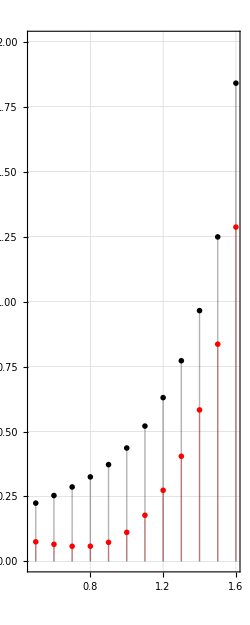
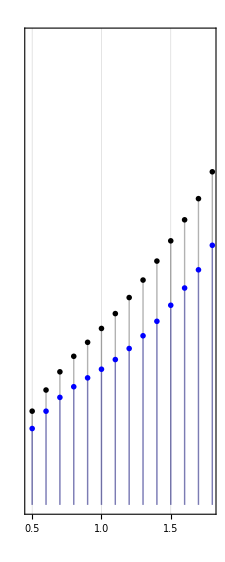

```mathematica
Row[{
ListPlot[{ΔBSE$GW3,ΔdBSE$GW3},Filling->Axis,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,12},PlotRange->{All,{0,2}},AspectRatio->2.5,FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{MaTeX["\\text{Error wrt FCI for b $^3\\Sigma_u^+$ (eV)}",FontSize->20],None},{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],None}},
ImageSize->250,
PlotStyle->{Red,Black},
PlotMarkers->"OpenMarkers",
PlotLegends->Placed[{MaTeX["\\text{BSE@$G_0W_0$}",FontSize->20],MaTeX["\\text{dBSE@$G_0W_0$}",FontSize->20]},{Left,Top}],
GridLines->Automatic]
,
ListPlot[{ΔBSE$GT3,ΔdBSE$GT3},Filling->Axis,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,12},PlotRange->{All,{0,2}},AspectRatio->2.5,FrameTicks->{{None,Automatic},{Automatic,None}},
FrameLabel->{{None,MaTeX["\\text{Error wrt FCI for b $^3\\Sigma_u^+$ (eV)}",FontSize->20]},{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],None}},
ImageSize->225,
PlotStyle->{Blue,Black},
PlotMarkers->"OpenMarkers",
PlotLegends->Placed[{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20],MaTeX["\\text{dBSE@$G_0T_0$}",FontSize->20]},{Left,Top}],
GridLines->Automatic]
}]
Export["H2_dBSE3.pdf",%];
```

# BeH_2/cc-pVDZ

## Singlets & Triplets

### Loading data for singlets

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

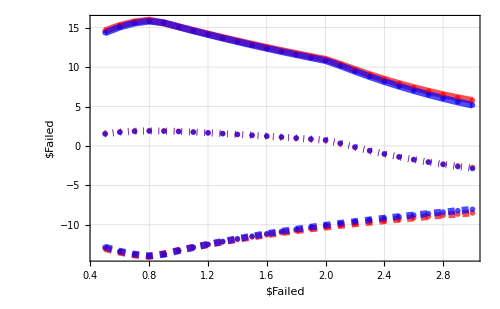

```mathematica
FCI1=Import["beh2_cc-pvdz_fci_singlets.dat"];
BSE$GT1=Import["beh2_cc-pvdz_bse@gt_singlets.dat"];
BSE$GW1=Import["beh2_cc-pvdz_bse@gw_singlets.dat"];
dBSE$GT1=Import["beh2_cc-pvdz_dbse@gt_singlets.dat"];
dBSE$GW1=Import["beh2_cc-pvdz_dbse@gw_singlets.dat"];
```

### Plotting stuff for singlets

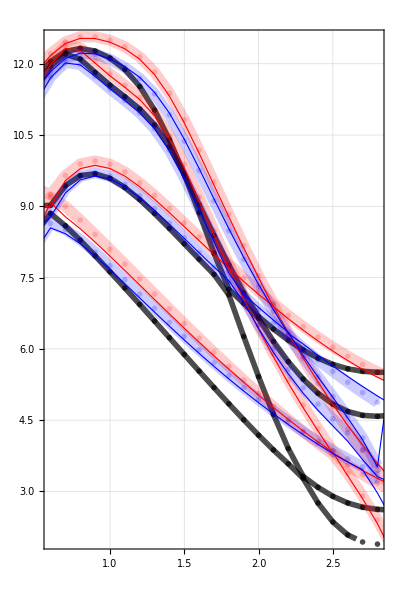

```mathematica
singlets=Show[{
ListPlot[
{FCI1⟦;;,{1,2}⟧,FCI1⟦;;,{1,3}⟧,FCI1⟦;;,{1,4}⟧,FCI1⟦;;,{1,5}⟧}
,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},AspectRatio->1.5,PlotRange->{{0.6,2.8},{2,12.5}},
FrameLabel->{MaTeX["R_{\\ce{Be-H}}~(\\AA)",FontSize->20],MaTeX["\\text{Singlet excitation energy (eV)}",FontSize->20]},
ImageSize->400,PlotStyle->Directive[{Black,Opacity[0.7],Thickness[0.01]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{FCI}",FontSize->20]},GridLines->Automatic]
,
ListPlot[
{BSE$GW1⟦;;,{1,2}⟧,BSE$GW1⟦;;,{1,3}⟧,BSE$GW1⟦;;,{1,4}⟧,BSE$GW1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0W_0$}",FontSize->20]}]
,
ListPlot[
{BSE$GT1⟦;;,{1,2}⟧,BSE$GT1⟦;;,{1,3}⟧,BSE$GT1⟦;;,{1,4}⟧,BSE$GT1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20]}]
,
ListPlot[
{dBSE$GW1⟦;;,{1,2}⟧,dBSE$GW1⟦;;,{1,3}⟧,dBSE$GW1⟦;;,{1,4}⟧,dBSE$GW1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[1.0],Thickness[0.002]}],PlotMarkers->None,Joined->True,PlotLegends->{MaTeX["\\text{dBSE@$G_0T_0$}",FontSize->20]}]
,
ListPlot[
{dBSE$GT1⟦;;,{1,2}⟧,dBSE$GT1⟦;;,{1,3}⟧,dBSE$GT1⟦;;,{1,4}⟧,dBSE$GT1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[1.0],Thickness[0.002]}],PlotMarkers->None,Joined->True,PlotLegends->{MaTeX["\\text{dBSE@$G_0T_0$}",FontSize->20]}]
}]
```

### Loading data for triplets

```mathematica
FCI3=Import["beh2_cc-pvdz_fci_triplets.dat"];
BSE$GT3=Import["beh2_cc-pvdz_bse@gt_triplets.dat"];
BSE$GW3=Import["beh2_cc-pvdz_bse@gw_triplets.dat"];
dBSE$GT3=Import["beh2_cc-pvdz_dbse@gt_triplets.dat"];
dBSE$GW3=Import["beh2_cc-pvdz_dbse@gw_triplets.dat"];
```

### Plotting stuff for triplets

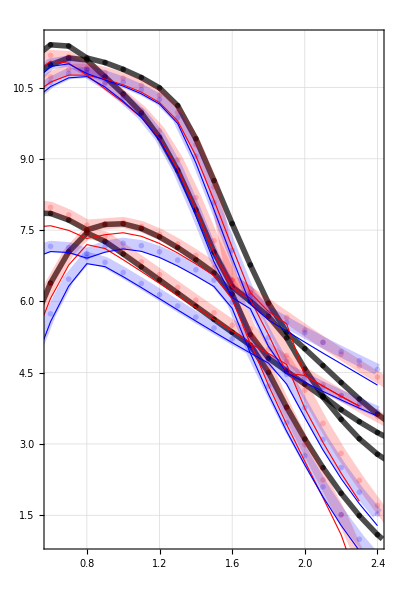

```mathematica
triplets=Show[{
ListPlot[
{FCI3⟦;;,{1,2}⟧,FCI3⟦;;,{1,3}⟧,FCI3⟦;;,{1,4}⟧,FCI3⟦;;,{1,5}⟧}
,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},AspectRatio->1.5,PlotRange->{{0.6,2.4},{1,11.5}},
FrameLabel->{MaTeX["R_{\\ce{Be-H}}~(\\AA)",FontSize->20],MaTeX["\\text{Triplet excitation energy (eV)}",FontSize->20]},
ImageSize->400,PlotStyle->Directive[{Black,Opacity[0.7],Thickness[0.01]}],PlotMarkers->"OpenMarkers",Joined->True,GridLines->Automatic]
,
ListPlot[
{BSE$GW3⟦;;,{1,2}⟧,BSE$GW3⟦;;,{1,3}⟧,BSE$GW3⟦;;,{1,4}⟧,BSE$GW3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True]
,
ListPlot[
{BSE$GT3⟦;;,{1,2}⟧,BSE$GT3⟦;;,{1,3}⟧,BSE$GT3⟦;;,{1,4}⟧,BSE$GT3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True]
,
ListPlot[
{dBSE$GW3⟦;;,{1,2}⟧,dBSE$GW3⟦;;,{1,3}⟧,dBSE$GW3⟦;;,{1,4}⟧,dBSE$GW3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[1.0],Thickness[0.002]}],PlotMarkers->None,Joined->True]
,
ListPlot[
{dBSE$GT3⟦;;,{1,2}⟧,dBSE$GT3⟦;;,{1,3}⟧,dBSE$GT3⟦;;,{1,4}⟧,dBSE$GT3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[1.0],Thickness[0.002]}],PlotMarkers->None,Joined->True]
}]
```

### Main graph

```mathematica
Grid[{{singlets,triplets}}]
Export["BeH2.pdf",%];
```

-Graphics- | -Graphics-

### Gap

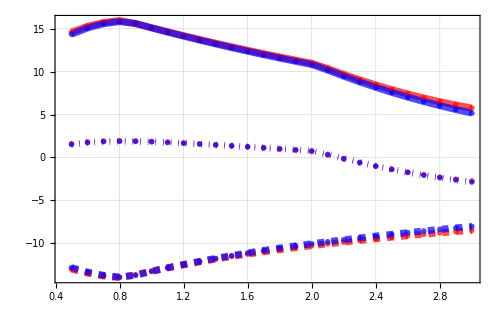

```mathematica
Gap=Import["beh2_cc-pvdz_gap.dat"];
ListPlot[{Gap⟦;;,{1,2}⟧,Gap⟦;;,{1,5}⟧,Gap⟦;;,{1,3}⟧,Gap⟦;;,{1,6}⟧,Gap⟦;;,{1,4}⟧,Gap⟦;;,{1,7}⟧},Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},PlotRange->{All,All},
FrameLabel->{MaTeX["R_{\\ce{Be-H}}~(\\AA)",FontSize->20],MaTeX["\\text{One-electron energy (eV)}",FontSize->20]},
ImageSize->500,
PlotStyle->{{Red,Dashed,Opacity[0.7],Thickness[0.01]},{Blue,Dashed,Opacity[0.7],Thickness[0.01]},
{Red,Dotted,Opacity[0.7],Thickness[0.005]},{Blue,Dotted,Opacity[0.7],Thickness[0.01]},
{Red,Opacity[0.7],Thickness[0.01]},{Blue,Opacity[0.7],Thickness[0.01]}},
PlotMarkers->"OpenMarkers",Joined->True,
PlotLegends->{MaTeX["\\text{HOMO@$G_0W_0$}",FontSize->20],MaTeX["\\text{HOMO@$G_0T_0$}",FontSize->20],
MaTeX["\\text{LUMO@$G_0W_0$}",FontSize->20],MaTeX["\\text{LUMO@$G_0T_0$}",FontSize->20],
MaTeX["\\text{Gap@$G_0W_0$}",FontSize->20],MaTeX["\\text{Gap@$G_0T_0$}",FontSize->20]},
GridLines->Automatic]
Export["BeH2_gap.pdf",%];
```

# H_4/STO-6G

## Singlets & Triplets

### Loading data for singlets

```mathematica
BSE$GW1=Import["h4_sto-6g_bse@gw_singlets.dat"];
BSE$GT1=Import["h4_sto-6g_bse@gt_singlets.dat"];
```

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

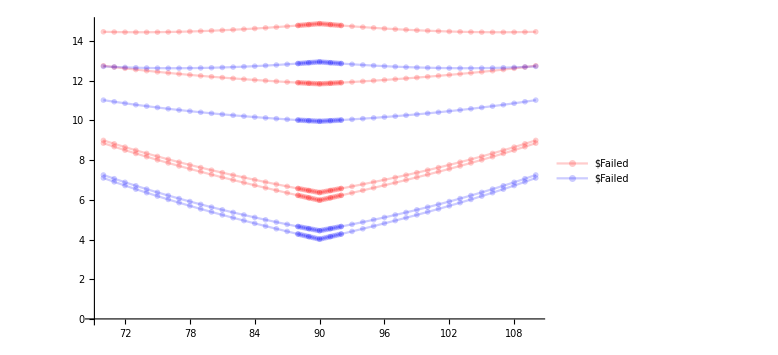

```mathematica
Show[{
ListPlot[
{BSE$GW1⟦;;,{1,2}⟧//Sort,BSE$GW1⟦;;,{1,3}⟧//Sort,BSE$GW1⟦;;,{1,4}⟧//Sort,BSE$GW1⟦;;,{1,5}⟧//Sort}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thick}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20]}]
,
ListPlot[
{BSE$GT1⟦;;,{1,2}⟧//Sort,BSE$GT1⟦;;,{1,3}⟧//Sort,BSE$GT1⟦;;,{1,4}⟧//Sort,BSE$GT1⟦;;,{1,5}⟧//Sort}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thick}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20]}]
}]
```

# Molecules

```mathematica
sB1={8.66, 6.61, 8.61, 7.70, 7.62, 6.84, 6.80}- 7.53;
sA2={10.34, 8.33, 10.30, 9.41, 9.34, 8.60, 8.56}-9.32;
tB1={7.98, 6.69, 7.86, 7.23, 7.09, 6.30, 6.23}- 7.14;
tA2={10.01, 8.70, 9.89, 9.22, 9.11, 8.36, 8.29}- 9.14;
method={"CIS","CIS(D)","TDHF","BSE@$G_0W_0$","dBSE@$G_0W_0$","BSE@$G_0T_0$","dBSE$G_0T_0$","",
"CIS","CIS(D)","TDHF","BSE@$G_0W_0$","dBSE@$G_0W_0$","BSE@$G_0T_0$","dBSE$G_0T_0$","",
"CIS","CIS(D)","TDHF","BSE@$G_0W_0$","dBSE@$G_0W_0$","BSE@$G_0T_0$","dBSE$G_0T_0$","",
"CIS","CIS(D)","TDHF","BSE@$G_0W_0$","dBSE@$G_0W_0$","BSE@$G_0T_0$","dBSE$G_0T_0$"};
```

```mathematica
Show[{
BarChart[{Callout[sB1,"^1B_1"],Callout[sA2,"^1A_2"],Callout[tA2,"^3B_1"],Callout[tA2,"^3A_2"]},ChartBaseStyle->EdgeForm[{Black,Thick}],ChartStyle->"Pastel"]
},
Frame->True,Axes->False,PlotRange->{All,{-1,1.6}},GridLines->{None,Automatic},FrameTicks->{{Automatic,None},{Table[{k+2/4,Rotate[MaTeX["\\text{"<>method⟦k⟧<>"}",FontSize->20],π/2]},{k,Length[method]}],None}},
BaseStyle->16,PlotRangePadding->0.5,FrameStyle->Directive[Thick,16,Black],AspectRatio->1/6,FrameLabel->{None,MaTeX["\\text{Error wrt FCI (eV)}",FontSize->24]},ChartStyle->ColorData[1,"PrivateStandardNames"][[1,2]],ImageSize->1000,Padding->True]
```

-Graphics-